## MAE 280 B - Linear Control Design Mauricio de Oliveira State Estimation

```mathematica
Hyperlink["http://fccr.ucsd.edu/~mauricio/courses/mae280b"]
```

# Estimator with GPS

## Problem Data

```mathematica
m = 100. (* 100 kg *);
```

```mathematica
A = {
{0,1},

{0,0}
};
Bw = {
{0},
{1/m}
};
Cy={
{1,0},
{0,0}
};
Dyw={
{0},
{0}
};
```

```mathematica
linearizedSystem=StateSpaceModel[{A,Bw,Cy,Dyw}]
```

(0 | 1 | 0
0 | 0 | 0.01
1 | 0 | 0
0 | 0 | 0)_^𝒮

```mathematica
Ww={{1^2}};
Wv={{10^2,0},{0,(10/1000)^2}}; (* 1 mg *)
```

## Filter design using Kalman

```mathematica
filterGPS= KalmanEstimator[linearizedSystem, {Ww, Wv}]
```

(-0.0447214 | 1. | 0.0447214 | 0.
-0.001 | 0. | 0.001 | 0.
1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
1. | 0. | 0. | 0.
0. | 0. | 0. | 0.)_^𝒮

```mathematica
F = -Normal[filterGPS][[2]];
MatrixForm[F]
```

(-0.0447214 | 0.
-0.001 | 0.)

Error Dynamics

```mathematica
Eigenvalues[A+ F.Cy]
```

{-0.0223607+0.0223607 ⅈ,-0.0223607-0.0223607 ⅈ}

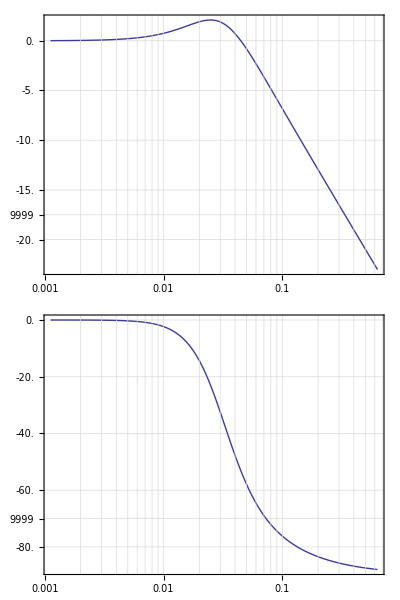

```mathematica
BodePlot[SystemsModelExtract[filterGPS,{1},{1}],GridLines->Automatic]
```

## Analysis of the filter

### Augment system with measurement noise input

```mathematica
Bwa=ArrayFlatten[{{Bw,ConstantArray[0,{2,2}]}}];
Dywa=ArrayFlatten[{{Dyw,IdentityMatrix[2]}}];
```

```mathematica
augmentedSystemGPS=StateSpaceModel[{A,Bwa,Cy,Dywa}]
```

(0 | 1 | 0 | 0 | 0
0 | 0 | 0.01 | 0 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)_^𝒮

### Simulate

```mathematica
h=.01;
```

```mathematica
Tmax = 600;
T = Table[i,{i,0,Tmax,h}];
w = MapThread[Flatten[{#1,#2}]&,{RandomVariate[NormalDistribution[],{Length[T],1}].MatrixPower[Ww,.5],RandomVariate[NormalDistribution[],{Length[T],2}].MatrixPower[Wv,.5]}];
```

Estimate stationary position

```mathematica
x0 = {0,0};
xhat0 = {0,0};
```

```mathematica
sysDiscreteGPS = ToDiscreteTimeModel[augmentedSystemGPS,h];
filterDiscreteGPS = ToDiscreteTimeModel[filterGPS,h];
```

```mathematica
{ySys,tSys,xSys}= {OutputResponse[{sysDiscreteGPS,x0},Transpose[w]],T,StateResponse[{sysDiscreteGPS,x0},Transpose[w]]};
```

```mathematica
{yFilterGPS,tFilterGPS,xFilterGPS}= {OutputResponse[{filterDiscreteGPS,xhat0},ySys],T,StateResponse[{filterDiscreteGPS,xhat0},ySys]};
```

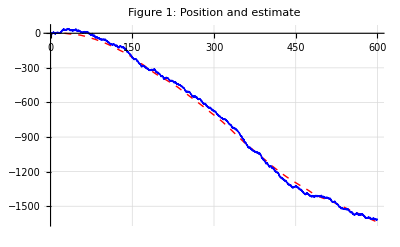

```mathematica
plots={{tSys,xSys[[1]]},{tFilterGPS,xFilterGPS[[1]]}};
plots=Map[Transpose,plots];
ListPlot[plots,PlotLabel->"Figure 1: Position and estimate",Joined->True,PlotStyle->{{Red,Dashed},Blue},GridLines->Automatic,PerformanceGoal->"Speed",MaxPlotPoints->2000]
```

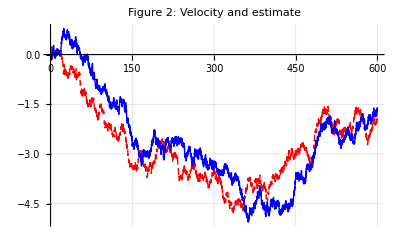

```mathematica
plots={{tSys,xSys[[2]]},{tFilterGPS,xFilterGPS[[2]]}};
plots=Map[Transpose,plots];
ListPlot[plots,PlotLabel->"Figure 2: Velocity and estimate",Joined->True,PlotStyle->{{Red,Dashed},Blue},GridLines->Automatic,PerformanceGoal->"Speed",MaxPlotPoints->2000]
```

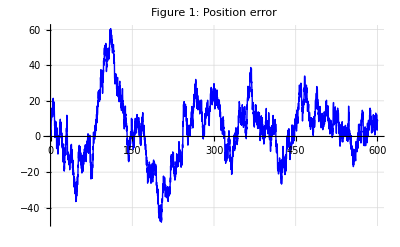

```mathematica
plots={{t,xSys[[1]]-xFilterGPS[[1]]}};
plots=Map[Transpose,plots];
ListPlot[plots,PlotLabel->"Figure 1: Position error",Joined->True,GridLines->Automatic,PlotStyle->{Blue},PerformanceGoal->"Speed",MaxPlotPoints->2000]
```

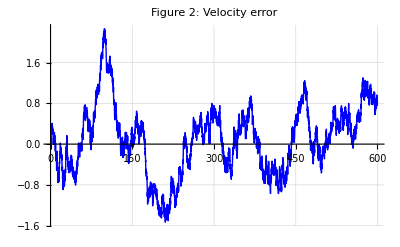

```mathematica
plots={{t,xSys[[2]]-xFilterGPS[[2]]}};
plots=Map[Transpose,plots];
ListPlot[plots,PlotLabel->"Figure 2: Velocity error",Joined->True,PlotStyle->{Blue},GridLines->Automatic,PerformanceGoal->"Speed",MaxPlotPoints->2000]
```

# Estimator with Accelerometer

## Problem Data

```mathematica
m = 100. (* 100 kg *);
```

```mathematica
A = {
{0,1},
{0,0}
};
Bw = {
{0},
{1/m}
};
CyGPS={
{1,0}
};
DywGPS={
{0}
};
```

### Accelerometer

```mathematica
CyA={{0,1}}.A;
DywA={{0,1}}.Bw;
```

```mathematica
Cy=ArrayFlatten[{{CyGPS},{CyA}}];
Dyw=ArrayFlatten[{{DywGPS},{DywA}}];
```

```mathematica
linearizedSystem=StateSpaceModel[{A,Bw,Cy,Dyw}]
```

(0 | 1 | 0
0 | 0 | 0.01
1 | 0 | 0
0 | 0 | 0.01)_^𝒮

```mathematica
Ww={{1^2}};
Wv={{10^2,0},{0,(10/1000)^2}}; (* 1 mg *)
```

## Filter design using Kalman

```mathematica
filterA= KalmanEstimator[linearizedSystem, {Ww, Wv}]
```

(-0.037606 | 1. | 0.037606 | 0.
-0.000707107 | 0. | 0.000707107 | 0.5
1. | 0. | 0. | 0.
0. | 1. | 0. | 0.
1. | 0. | 0. | 0.
0. | 0. | 0. | 0.)_^𝒮

```mathematica
F = -Normal[filterA][[2]];
MatrixForm[F]
```

(-0.037606 | 0.
-0.000707107 | -0.5)

Error Dynamics

```mathematica
Eigenvalues[A+ F.Cy]
```

{-0.018803+0.018803 ⅈ,-0.018803-0.018803 ⅈ}

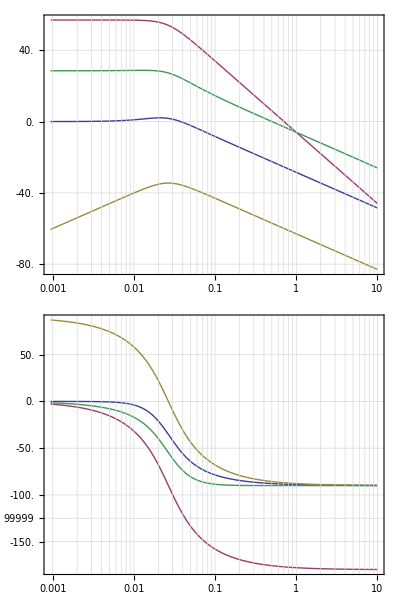

```mathematica
BodePlot[SystemsModelExtract[filterA,{1,2},{1,2}],GridLines->Automatic]
```

## Analysis of the filter

### Augment system with measurement noise input

```mathematica
Bwa=ArrayFlatten[{{Bw,ConstantArray[0,{2,2}]}}];
Dywa=ArrayFlatten[{{Dyw,IdentityMatrix[2]}}];
```

```mathematica
augmentedSystemA=StateSpaceModel[{A,Bwa,Cy,Dywa}]
```

(0 | 1 | 0 | 0 | 0
0 | 0 | 0.01 | 0 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 0.01 | 0 | 1)_^𝒮

### Simulate

```mathematica
x0 = {0,0};
xhat0 = {0,0};
```

```mathematica
sysDiscreteA = ToDiscreteTimeModel[augmentedSystemA,h];
filterDiscreteA = ToDiscreteTimeModel[filterA,h];
```

```mathematica
{ySys,tSys,xSys}= {OutputResponse[{sysDiscreteA,x0},Transpose[w]],T,StateResponse[{sysDiscreteA,x0},Transpose[w]]};
```

```mathematica
{yFilterA,tFilterA,xFilterA}= {OutputResponse[{filterDiscreteA,xhat0},ySys],T,StateResponse[{filterDiscreteA,xhat0},ySys]};
```

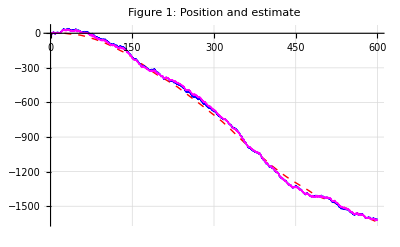

```mathematica
plots={{tSys,xSys[[1]]},{tSys,xFilterGPS[[1]]},{tSys,xFilterA[[1]]}};
plots=Map[Transpose,plots];
ListPlot[plots,PlotLabel->"Figure 1: Position and estimate",Joined->True,PlotStyle->{{Red,Dashed},Blue,Magenta},GridLines->Automatic,PerformanceGoal->"Speed",MaxPlotPoints->2000]
```

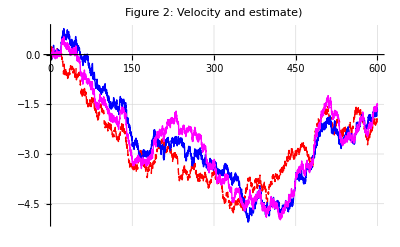

```mathematica
plots={{tSys,xSys[[2]]},{tSys,xFilterGPS[[2]]},{tSys,xFilterA[[2]]}};
plots=Map[Transpose,plots];
ListPlot[plots,PlotLabel->"Figure 2: Velocity and estimate)",Joined->True,PlotStyle->{{Red,Dashed},Blue,Magenta},GridLines->Automatic,PerformanceGoal->"Speed",MaxPlotPoints->2000]
```

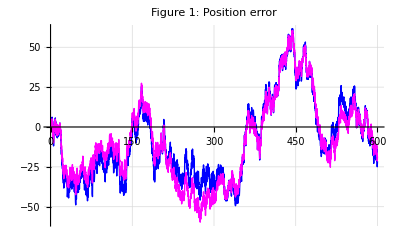

```mathematica
plots={{tSys,xSys[[1]]-xFilterGPS[[1]]},{tSys,xSys[[1]]-xFilterA[[1]]}};
plots=Map[Transpose,plots];
ListPlot[plots,PlotLabel->"Figure 1: Position error",Joined->True,PlotStyle->{Blue,Magenta},GridLines->Automatic,PerformanceGoal->"Speed",MaxPlotPoints->2000]
```

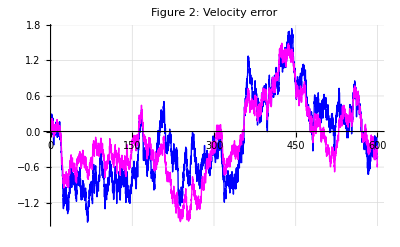

```mathematica
plots={{tSys,xSys[[2]]-xFilterGPS[[2]]},{tSys,xSys[[2]]-xFilterA[[2]]}};
plots=Map[Transpose,plots];
ListPlot[plots,PlotLabel->"Figure 2: Velocity error",Joined->True,PlotStyle->{Blue,Magenta},GridLines->Automatic,PerformanceGoal->"Speed",MaxPlotPoints->2000]
```